# How Mathematica improves my teaching

## Christopher R. H. Hanusa Queens College, CUNY

## Technology in Mathematics Instruction Conference June 8, 2010

## Motivating Examples

```mathematica
Integrate[1/(x^3+5),x]
```

(2 √3 ArcTan[(-5+2 5^(2/3) x)/(5 √3)]+2 Log[5+5^(2/3) x]-Log[5-5^(2/3) x+5^(1/3) x^2])/(6 5^(2/3))

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
Manipulate[ContourPlot3D[x^2+y^2+a z^3==1,{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None],{a,-2,2,.05},{a}]
```

## Graph Theory figures and animations

### Many graphs are built in to Mathematica.

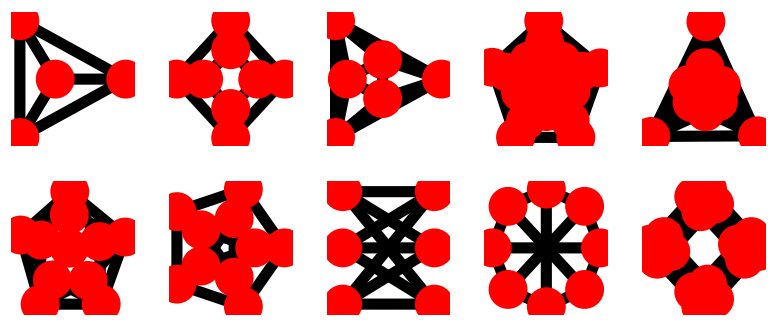

```mathematica
<< Combinatorica`
AllG =ShowGraphArray[{{TetrahedralGraph,CubicalGraph,OctahedralGraph,DodecahedralGraph,IcosahedralGraph},{GroetzschGraph,PetersenGraph,CompleteKPartiteGraph[3,3],Harary[3,8],Hypercube[4]}},VertexStyle->Disk[0.07],VertexColor->Red,EdgeStyle->Thick]
```

### Ford-Fulkerson Algorithm (Maximum Flow / Minimum Cut)

Goal: Given a network (a graph with capacity constraints), find the maximum flow from the start (s) to the finish (t)
Problem: Every figure takes long to draw, algorithm requires keeping track of many features.

```mathematica
GraphPlot[{{"s"->"a"," c_1=2 "},{"s"->"b"," c_2=3 "},{"a"->"c"," c_3=4 "},{"b"->"c"," c_4=1 "},{"b"->"d"," c_5=3 "},{"d"->"a"," c_6=2 "},{"c"->"t"," c_7=3 "},{"d"->"t"," c_8=4 "}}, VertexLabeling->True,VertexRenderingFunction->({White,EdgeForm[{Black,Thick}],Disk[#,.06],Black,Style[Text[#2,#1],Large,Italic,Bold]}&),
VertexCoordinateRules->{"s"->{0.25,0},"a"->{1,0.5},"b"->{1,-0.5},"c"->{2.25,0.5},"d"->{2.25,-0.5},"t"->{3,0}},DirectedEdges->True,EdgeRenderingFunction->(If[(#2=={"b","c"})||(#2=={"d","a"}),{Black,Thick,Arrowheads[{{0.03,1}}],Arrow[#1,0.05],Inset[Framed[Style[#3,Blue,Large,Italic, Bold]],Mean[{#1[[1]],Mean[#1]}],Automatic,Automatic,None,Background->White]},
{Black,Thick,Arrowheads[{{0.03,1}}],Arrow[#1,0.05],Inset[Framed[Style[#3,Blue,Large,Italic, Bold]],Mean[#1],Automatic,Automatic,None,Background->White]}]&),ImageSize->800];
Show[%,Graphics[{Thick, Red,Rotate[Circle[{0.6,0.25},{0.22,0.8}],0.67Pi]}]]
```

-Graphics-

Mathematica allows the creation of precise, detailed, colored slides.

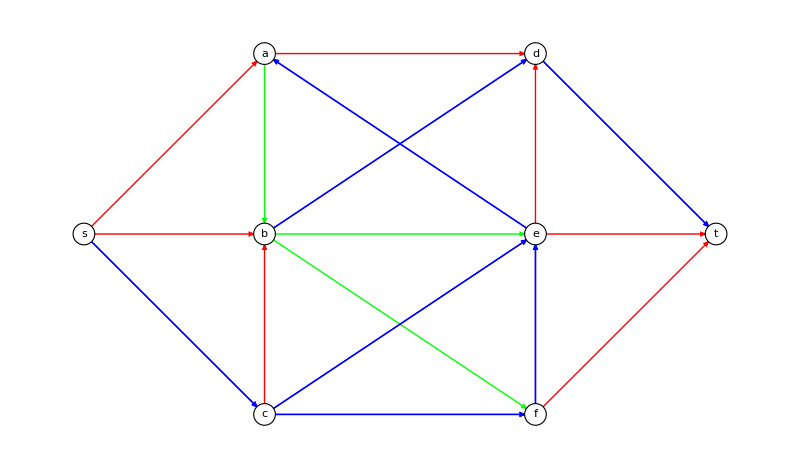

```mathematica
EmptyEdges={{"a","b"},{"b","e"},{"b","f"}};
AtCapacity={{"s","a"},{"s","b"},{"a","d"},{"e","t"},{"c","b"},{"e","d"},{"f","t"}};
GraphPlot[{{"s"->"a",{1,1}},{"s"->"b",{2,2}},{"s"->"c",{2,10}},{"a"->"b",{1,4}},{"c"->"b",{0,2 }},{"a"->"d",{0,2}},{"b"->"d",{2,7 }},{"b"->"e",{0,1 }},{"b"->"f",{0,2 }},{"c"->"e",{2,4 }},{"c"->"f",{0,5}},{"e"->"a",{0,2}},{"e"->"d",{0,2}},{"f"->"e",{0,5}},{"d"->"t",{3,11}},{"e"->"t",{2,2}},{"f"->"t",{0,1 }}}, VertexLabeling->True,VertexRenderingFunction->({White,EdgeForm[{Black,Thick}],Disk[#,.06],Black,Style[Text[#2,#1],Large,Italic,Bold]}&),
VertexCoordinateRules->{"s"->{0,0},"a"->{1,1},"b"->{1,0},"c"->{1,-1},"d"->{2.5,1},"e"->{2.5,0},"f"->{2.5,-1},"t"->{3.5,0}},EdgeRenderingFunction->(If[MemberQ[EmptyEdges,#2],
{Green,Thick,Arrowheads[{{.03,1}}],Arrow[#1,0.05]},If[MemberQ[AtCapacity,#2],{Red,Thick,Arrowheads[{{-0.03,0}}],Arrow[#1,0.05]},{Blue,Thick,Arrowheads[{{0.03,1}}],Arrow[#1,0.05],Arrowheads[{{-0.03,0}}],Arrow[#1,0.05]}]]&),ImageSize->800]
```

### Kempe Chain Argument in the Five-Color Theorem

Goal: Prove that the vertices of every planar graph can be (properly) colored with five colors.
Problem: The proof involves five colors and requires a large example.

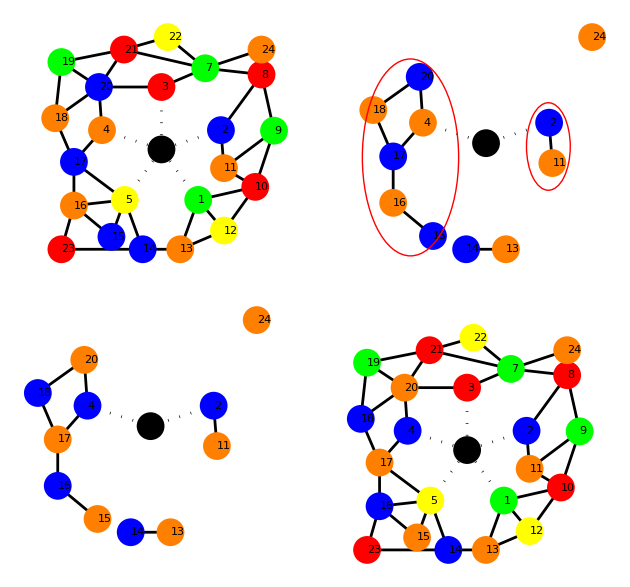

### The "Turning Trick", an aide in finding graph decompositions

Goal: Break down a complete graph into many copies of a smaller graph.
Application: Finding an assignment of players to matches in a tournament.
Problem: Requires many different sets of edges, understanding the "Turning"

```mathematica
<<Combinatorica`
(* Create a graph with nine vertices in a circle with one more vertex, no edges, rotated so that the last vertex is at the top. *)
G=RotateVertices[AddVertex[EmptyGraph[9],{1,-0.75}],Pi/2];  
(* Insert the edges for each family.  Room for improvement:  there should be a better algorithm to generate these edges in which case we could change 10 to any other number *)
EdgeList={
{{1,8},{2,7},{3,6},{4,5},{9,10}},{{1,6},{2,5},{3,4},{9,7},{8,10}},{{1,4},{2,3},{9,5},{6,8},{7,10}},{{1,2},{9,3},{8,4},{7,5},{6,10}},{{1,9},{2,8},{3,7},{4,6},{5,10}},{{1,7},{2,6},{3,5},{8,9},{4,10}},{{1,5},{2,4},{6,9},{7,8},{3,10}},{{1,3},{4,9},{5,8},{6,7},{2,10}},{{2,9},{3,8},{4,7},{5,6},{1,10}}};
(* Create a list of colors that corresponds to a rainbow.  Could have used
ColorList={Red,Orange,Yellow,LightGreen,Green,Cyan,Blue,Purple,Magenta}; but the command below is more sophisticated. *)
ColorList=Table[ColorData["Rainbow"][1-n/8],{n,0,8,1}];
(* Now see the different edge classes,each at a time. *)
For[n=1,n≤9,n++,
GG[n]=SetGraphOptions[AddEdges[G,EdgeList[[n]]],VertexLabel->{8,7,6,5,4,3,2,1,0,x}];
GG[n]=SetGraphOptions[GG[n],{Flatten[{EdgeList[[n]],EdgeColor->ColorList[[n]]},1]}](*;GG[n]=SetGraphOptions[GG[n],{Flatten[{Take[EdgeList[[n]],4],EdgeStyle->Thick},1]}]*)]
(*ShowGraph[GraphSum[GG[1],GG[2],GG[3]]]*)
{Manipulate[ShowGraph[GG[nn]],{nn,1,9,1}],
Manipulate[ShowGraph[Apply[GraphSum,Table[GG[i],{i,1,nn}]]],{nn,1,9,1}]}
```

{,}

```mathematica
(* Create a graph with eight vertices in a circle with one more vertex, no edges, rotated so that the last vertex is at the top. *)
G2=RotateVertices[AddVertex[EmptyGraph[8],{1,-0.75}],Pi/2];  
(* Insert the edges for each family.  Room for improvement:  there should be a better algorithm to generate these edges in which case we could change 10 to any other number *)
EdgeList2={
{{8,1},{1,7},{7,2},{2,6},{6,3},{3,5},{5,4},{4,9},{9,8}},
};
EdgeList2=Table[
{{Mod[8+i,8]+1,1+i+1},{1+i+1,Mod[7+i,8]+1},{Mod[7+i,8]+1,2+i+1},{2+i+1,Mod[6+i,8]+1},{Mod[6+i,8]+1,3+i+1},{3+i+1,5+i+1},{5+i+1,4+i+1},{4+i+1,9},{9,Mod[8+i,8]+1}},
{i,{-1,2,1,0}}];
(* Create a list of colors that corresponds to a rainbow.  Could have used
ColorList={Red,Orange,Yellow,LightGreen,Green,Cyan,Blue,Purple,Magenta}; but the command below is more sophisticated. *)
(*ColorList=Table[ColorData["Rainbow"][1-n/3],{n,0,3,1}];*)
ColorList2={Red,Green,Blue,Purple};
(* Now see the different edge classes,each at a time. *)
For[n=1,n≤4,n++,
(*GG[n]=SetGraphOptions[AddEdges[G,EdgeList[[n]]],VertexLabel->{1,2,3,4,5,6,7,8,9}];*)
GG2[n]=SetGraphOptions[AddEdges[G2,EdgeList2[[n]]],VertexLabel->{7,6,5,4,3,2,1,0,x}];
GG2[n]=SetGraphOptions[GG2[n],{Flatten[{EdgeList2[[n]],EdgeColor->ColorList[[n]]},1]}](*;GG[n]=SetGraphOptions[GG[n],{Flatten[{Take[EdgeList[[n]],4],EdgeStyle->Thick},1]}]*)]
(*ShowGraph[GraphSum[GG[1],GG[2],GG[3]]]*)
{Manipulate[ShowGraph[GG2[nn]],{nn,1,4,1}],
Manipulate[ShowGraph[Apply[GraphSum,Table[GG2[i],{i,1,nn}]]],{nn,1,4,1}]}
```

{,}

## Mathematical Modeling animations

### Linear Programming

Goal: Find the intersection of a number of halfspaces. (The feasible region)
Problem: Difficult to draw all halfspaces and shading.
Solution: Can see how adding a hyperplane chops the feasible region.

```mathematica
hyplist={x≥0,y≥0,4x+y≤10,18x+15y≤66};
Manipulate[GraphicsGrid[{{Show[{Plot[0,{x,-5,10},PlotRange->{-5,10},Frame->True,AspectRatio->1],If[h1,{Graphics[{Blue, Thick,Line[{{0,-5},{0,10}}]},PlotRange->{{-5,10},{-5,10}}],Graphics[{Blue,Opacity[0.3],Rectangle[{0,-5},{10,10}]},PlotRange->{{-5,10},{-5,10}}]},{}],If[h2,Plot[0,{x,-5,10},PlotRange->{-5,10},PlotStyle->{Thick,Red},Filling->Top,FillingStyle->Directive[Opacity[0.3],Red]],{}],If[h3,Plot[10-4x,{x,-5,10},PlotRange->{-5,10},PlotStyle->{Thick,Green},Filling->Bottom,FillingStyle->Directive[Opacity[0.3],Green]],{}],If[h4,Plot[(66-18x)/15,{x,-5,10},PlotRange->{-5,10},PlotStyle->{Thick,Purple},Filling->Bottom,FillingStyle->Directive[Opacity[0.3],Purple]],{}]}],RegionPlot[Apply[And,Part[hyplist,Flatten[{If[h1,1,{}],If[h2,2,{}],If[h3,3,{}],If[h4,4,{}]}]]],{x,-5,10},{y,-5,10},Axes->True,PlotPoints->10,BoundaryStyle->Thick]}},ImageSize->600],{{h3,False,Style[hyplist[[3]],Large]},{True,False}},{{h4,False,Style[hyplist[[4]],Large]},{True,False}},{{h1,True,Style[hyplist[[1]],Large]},{True,False}},{{h2,True,Style[hyplist[[2]],Large]},{True,False}}]
```

Goal: Find the optimal value of linear program graphically
Problem: Difficult to understand that solution is only dependent on objective function.
Solution: Create a Manipulate command which allows modification of function.

```mathematica
Manipulate[Show[{Plot[0,{x,-1,5},PlotRange->{-1,5},Frame->True,AspectRatio->1],If[plot,Plot[(c-a x)/b,{x,-1,5},PlotRange->{-1,5},PlotStyle->{Red,Thick}],{}],Graphics[{Black,Disk[{0,66/15},.1],Style[Text["(0,66/15)",{0+.4,66/15+.3}],"Large"],Disk[{0,0},.1],Style[Text["(0,0)",{0-.4,0-.4}],"Large"],Disk[{2.5,0},.1],Style[Text["(2.5,0)",{2.5+.4,0-.4}],"Large"],Disk[{2,2},.1],Style[Text["(2,2)",{2+.4,2+.4}],"Large"]}],Graphics[{Blue,EdgeForm[Directive[Thick,Blue]],Opacity[0.3],Polygon[{{0,0},{2.5,0},{2,2},{0,66/15}}]},PlotRange->{{-5,10},{-5,10}}]},ImageSize->400],{{plot,True,Style["Show Line ax+by=k",Large]},{True,False}},{{a,1000,Style["Value of a",Large]},Range[-1000,1000,100]},{{b,500,Style["Value of b",Large]},Drop[Range[-1000,1000,100],{11}]},{{c,2000,Style["Slider for k",Large]},Range[-5000,5000,100],ControlType->Slider},{{c,2000,Style["Value of k",Large]},ControlType->InputField}]
```

### Simulation of a random event: Coin Toss

Shows: Simulating multiple times gives different results.

```mathematica
Table[If[RandomInteger[]==0,"Head","Tail"],{20}]
BarChart[Partition[Tally[%][[All,2]],2],ChartLabels->{Placed[{Style["Tails",Large],Style["Heads",Large]},Center]}]
```

{Tail,Tail,Head,Head,Tail,Tail,Head,Head,Tail,Tail,Tail,Head,Head,Tail,Head,Tail,Tail,Tail,Head,Tail}

-Graphics-

### Monte Carlo Simulation: Approximation of π

Goal:  Determine the area of a unknown region.
Idea: Randomly place points in a surrounding rectangle. 

(points in the region)/(points in the rectangle)≈(area of region)/(area of rectangle)

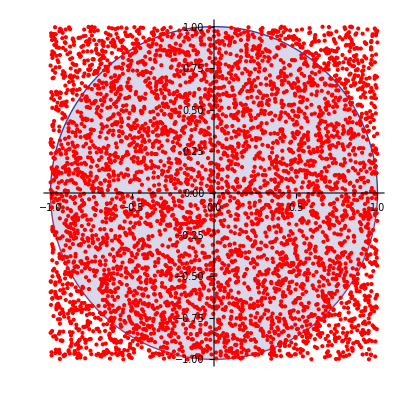

3.1016

```mathematica
region=Plot[{Sqrt[1-x^2],-Sqrt[1-x^2]}, {x, -1, 1},Filling->{1->{2}},AspectRatio->1];
points=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{i,5000}];
dots=ListPlot[points,PlotStyle->{Red,PointSize->Small}];
Show[region,dots]
Length[Select[points,(#[[1]]^2+#[[2]]^2≤1)&]]/5000.*4
```

### Queuing Model: Simulating a Waiting Room

Goal:  Understand dynamics of a waiting room
Idea: Every minute between 9am and noon a patient arrives with probability 7.5%.  
          Each patient needs 15 minutes with the doctor
Questions:  How many patients are left at the end of the day?
                    How much of the day is the doctor busy?
                    What happens if you modify parts of the simulation?

How many patients are left at the end of the day?

```mathematica
trials=Table[nwait=0;busy=0;endTime=0;
For[i=0,i<180,i++,If[endTime==i,busy=0];
newPatient=If[RandomReal[]≤0.075,1,0];
If[newPatient==1,nwait++];
If[busy==0&&nwait>0,nwait--;busy=1;endTime=i+15];];
nwait,{j,1000}];
Print["1000-trial average:  " <>ToString[N[Mean[trials]]] <> " patients waiting"]
Histogram[trials]
```

1000-trial average:  3.064 patients waiting

-Graphics-

What percentage of the day is the doctor busy?

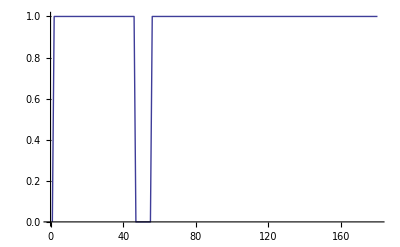

This trial:  94.4444 %

100-trial avg:  85.1167 %

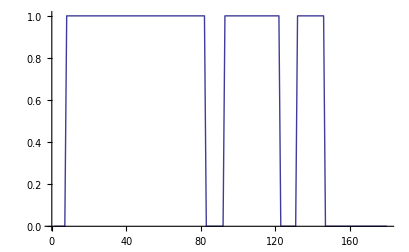
-Graphics-
This trial:  66.6667 %
100-trial avg:  83.4611 %

```mathematica
nwait=0;busy=0;endTime=0;
For[i=0,i<180,i++,If[endTime==i,busy=0];
newPatient=If[RandomReal[]≤0.075,1,0];
If[newPatient==1,nwait++];
If[busy==0&&nwait>0,nwait--;busy=1;endTime=i+15];
isBusy[i]=busy;];
busyList=Table[isBusy[i],{i,0,179}];
ListLinePlot[busyList,PlotStyle->Thick]
Print["This trial:  " <> ToString[N[Total[busyList]/180*100]]<>" %"];
Mean[Table[nwait=0;busy=0;endTime=0;
For[i=0,i<180,i++,If[endTime==i,busy=0];
newPatient=If[RandomReal[]≤0.075,1,0];
If[newPatient==1,nwait++];
If[busy==0&&nwait>0,nwait--;busy=1;endTime=i+15];
isBusy[i]=busy;];
Total[Table[isBusy[i],{i,0,179}]];,{500}]]
Print["100-trial avg:  " <> ToString[Mean[Table[nwait=0;busy=0;endTime=0;
For[i=0,i<180,i++,If[endTime==i,busy=0];
newPatient=If[RandomReal[]≤0.075,1,0];
If[newPatient==1,nwait++];
If[busy==0&&nwait>0,nwait--;busy=1;endTime=i+15];
isBusy[i]=busy;];
Total[Table[isBusy[i],{i,0,179}]],{100}]]/180*100.]<>" %"];
```

## Examples of student projects from Math with Mathematica

### Sameed Ahmed: Where can I move?

```mathematica
MyPawn[{x_,y_}]:=Select[Flatten[Table[{{x,y+i}},{i,1}],1],(0≤First[#]≤7&&0≤Last[#]≤7)&]
OpponentPawn[{x_,y_}]:=Select[Flatten[Table[{{x+i,y-i},{x-i,y-i}},{i,1}],1],(0≤First[#]≤7&&0≤Last[#]≤7)&]
(*Although it may seem unnecessary to create a table for "Opponent Pawn" that goes from i=1 to 1 when I could have simply put "y+1" instead, I need to use Table because it creates a different kind of list which allows for it to be compared when using Compliment. Also, unlike for other pieces, the pawn is defined for me and the opponent because it is the only piece for which there are different movements for each player. From my perspective, my pawn can only move up, and my opponent's pawn can only move down. Moreover, one may notice that the two pawns have different movements. This is as such because my project is only concerned with not being eaten. Since a pawn can only move forward one space and only eat diagonally one space, my pawn is concerned with moving without being eaten, and my opponent's pawn is concerned with eating another piece.*)
Rook[{x_,y_}]:=Select[Flatten[Table[{{x+i,y},{x-i,y},{x,y+i},{x,y-i}},{i,1,7}],1],(0≤First[#]≤7&&0≤Last[#]≤7)&]
Knight[{x_,y_}]:=Select[{{x+1,y+2},{x-1,y+2},{x+1,y-2},{x-1,y-2},{x+2,y+1},{x-2,y+1},{x+2,y-1},{x-2,y-1}},(0≤First[#]≤7&&0≤Last[#]≤7)&]
Bishop[{x_,y_}]:=Select[Flatten[Table[{{x+i,y+i},{x-i,y+i},{x+i,y-i},{x-i,y-i}},{i,1,7}],1],(0≤First[#]≤7&&0≤Last[#]≤7)&]
Queen[{x_,y_}]:=Select[Flatten[{Rook[{x,y}],Bishop[{x,y}]},1],(0≤First[#]≤7&&0≤Last[#]≤7)&]
(*A queen's movement is the combination of the movement of a rook and a bishop.*)
ExtraKing[{x_,y_}]:=Flatten[Table[{{x+i,y},{x-i,y},{x+i,y+i},{x-i,y+i},{x,y-i}},{i,1}],1]
King[{x_,y_}]:=Select[Flatten[{MyPawn[{x,y}],OpponentPawn[{x,y}],ExtraKing[{x,y}]},1],(0≤First[#]≤7&&0≤Last[#]≤7)&]
(*A king's movement is the combination of the movemnt of the pawns that I defined and some extra spots covered by "ExtraKing."*)
Manipulate[
GraphicsGrid[
{{If[(x1==x2&&y1==y2),Style["Two pieces cannot simultaneously occupy the same spot!",FontSize->24],GraphicsGrid[
Table[
Graphics[
{If[OddQ[i+j],Black,White],Rectangle[],
If[MemberQ[Complement[MyPiece[{x1,y1}],OpponentPiece[{x2,y2}]],{j,i}],{Green,Disk[{0.5,0.5},.4]},{}],
If[{x1,y1}=={j,i},{Blue,Disk[{0.5,0.5},.4]},{}],
If[{x2,y2}=={j,i},{Red,Disk[{0.5,0.5},.4]},{}]},ImageSize->50],
{i,0,7},{j,0,7}],
Frame->All]]},
{GraphicsGrid[
{{Graphics[{Blue,Disk[{0.2,0.2},.2]},ImageSize->{100,50}], Style["My piece.",FontSize->16]},{Graphics[{Green,Disk[{0.2,0.2},.2]},ImageSize->50], Style["Where I can move.",FontSize->16]},{Graphics[{Red,Disk[{0.2,0.2},.2]},ImageSize->50], Style["The opponent's piece.",FontSize->16]}}]}}],
{MyPiece,{MyPawn,Rook,Knight,Bishop,Queen,King}},{{x1,0,"My Position X"},0,7,1},{{y1,0,"My Position Y"},0,7,1},{OpponentPiece,{OpponentPawn,Rook,Knight,Bishop,Queen,King}},{{x2,0,"Opponent Position X"},0,7,1},{{y2, 0,"Opponenet Position Y"},0,7,1}]
(*Spaces were added to make this congested code readable. One may notice that Table, which iterates this boxes on the board, is in the form {i,j}. However, the If statement is in the form {j,i}. This as such because Table makes the first row i, and each column j, but the output list is in the form {x,y}, where x is the horizontal axis, and y is the vertical axis. Thus the i and j had to be switched. In this board, the top left box is {0,0} and the bottom right is {7,7}. To make the picture neat, font and image sizes were edited.*)
```

### Jin Shen Yap : An introduction to the Abacus

### Jin You: The Mean value Theorem

```mathematica
f[x_]:=(x+2)(x-1)(x-3)
Manipulate[
If[d≠b,
Show[
Plot[f[x],{x,-2.5,3},AxesLabel->"f[x]=(x+2)(x-1)(x-3)",PlotRange->{-10,10},PlotStyle->{Thick,Blue}],(*Plot orioginal fuction*)
Graphics[Point[{d,f[d]}]], (* To display the point (a,f(a) *)
Graphics[Text[Style[{"a=",d},Medium,Italic,Orange],{d,f[d]}]], (*To display the 'a' vlues as a text *)
Graphics[Point[{b,f[b]}]], (* To display the point (b,f(b)) *)
Graphics[Text[Style[{"b=",b},Medium,Italic,Orange],{b,f[b]}]], (*To display the 'b' values as a text*)
Graphics[{Thick,Green,Dashed,Line[{{d,f[d]},{b,f[b]}}]}],(*To display line between point 'a' and 'b'*)
Graphics[Point[{c,f[c]}]/.First[Solve[f'[ c]==((f[d]-f[b])/(d-b)),c]]],(*To display the point (c,f(c))*)
Graphics[Text[Style[{"c=",c},Medium,Bold,Red],{c, f[c]}]/.First[Solve[f'[ c]==((f[d]-f[b])/(d-b)),c]]],(*To display 'c' values in given formular*)
Plot[LT[x,c]/.First[Solve[f'[c]==((f[d]-f[b])/(d-b)),c]],{x,-2,3},PlotRange->{-10,10},PlotStyle->{Thick,Pink,Dashed}],(*To display the tangent line*)
Graphics[Point[{e,f[e]}]/.Last[Solve[f'[ e]==((f[d]-f[b])/(d-b)),e]]],(*To display another point (c,f(c))*)
Graphics[Text[Style[{"d=",e},Medium,Bold,Red],{e, f[e]}]/.Last[Solve[f'[e]==((f[d]-f[b])/(d-b)),e]]],(*Change plotstyle*)
Plot[LT[x,e]/.Last[Solve[f'[e]==((f[d]-f[b])/(d-b)),e]],{x,-2,3},PlotRange->{-10,10},PlotStyle->{Thick,Pink,Dashed}](*To display the tangent line*)
],
"Error! a=b!"],(*To show the error message when a=b*)
{{d,-2,"a"},-2,3},{{b,2.5},-2,3},ControlPlacement->Left](*Make Manipulate Controlplacement to the Left.*)
```